# Classification and Prediction of Water/Steam Properties using data from IF-97 Industrial Standard

## Aneet Dharmavaram Narendranath, PhD

Join the Conversation #WolframTechConf

## ABSTRACT: For ζ ϵ (P,T) and h ϵ C, find classifier f: ζ → C

Pedagogically, the interpolation of specific enthalpy data may be treated as a classification problem.  I utilize the Classify and Predict functions for thermodynamic properties of water.  The objective is to create a classifier and a complementary prediction object to evaluate the power output of a steam turbine, given the inlet and outlet (-to the turbine) steam states.

Specific enthalpies (h, kJ/kg) of steam as a function of pressure (P, bar) and temperature (T, Celsius) are imported.  In addition to the specific enthalpy, regions of water’s P-T phase diagram are also imported.  These regions are per the industrial standard IAPWS IF-97.  Mathematica’s Classify is used to check which numerical algorithm best classifies the (P,T) tuples into regions.  This algorithm is then used to create a prediction object for (P,T) → h which is then used to evaluate the power produced by a steam turbine, which is a fundamental building block in thermodynamics.

## Some Notes regarding treatment presented here

Treating this as a classification and Decision Tree problem allows for a high-level human orientated description of how zones of pressure and temperature are associated with different magnitudes of thermodynamic properties.  This may be exploited towards intuitive thermodynamic system design towards higher thermal efficiency.

Treatment of evaluation of specific enthalpy using a decision tree model allows for intuitive move from steam tables to ML model.

There have been some other works on using ML for thermodynamics: Sencan (2006, 2011) [Performance of Ammonia/Water absorption refrigeration system], Yousefi (2017) [ANN to predict thermodynamic properties of pure and mixtures of alkali metals]

Previous work used equation of state described for entire region of P,T.  Coupled set of equations.

## ‘Hello World’ of Classification: Iris Dataset

The Fisher Iris dataset is imported from one of the many online repositories.

```mathematica
url="https://raw.githubusercontent.com/jbrownlee/Datasets/master/iris.csv";
dataset=Import[url];
```

### Probing the dataset to visually ascertain dimensions and identify features

“The dataset contains a set of 150 records under five attributes - petal length, petal width, sepal length, sepal width and species.”

```mathematica
(*names={'sepal-length','sepal-width','petal-length','petal-width','class'}*)
Dimensions[dataset]
dataset[[1;;5]]
dataset[[All,5]]//Tally
```

{150,5}

{{5.1,3.5,1.4,0.2,Iris-setosa},{4.9,3.,1.4,0.2,Iris-setosa},{4.7,3.2,1.3,0.2,Iris-setosa},{4.6,3.1,1.5,0.2,Iris-setosa},{5.,3.6,1.4,0.2,Iris-setosa}}

{{Iris-setosa,50},{Iris-versicolor,50},{Iris-virginica,50}}

## Data distribution into bins and Clustering

```mathematica
sepalLength=dataset[[All,1]];
petalLength=dataset[[All,3]];
petalWidth=dataset[[All,4]];
sepalWidth=dataset[[All,2]];
class=dataset[[All,5]]/.{"Iris-setosa"->"setosa", "Iris-versicolor"->"versicolor", "Iris-virginica"->"virginica"};
```

#### Three dimensional/quantitative subsets of data are explored to reveal positive correlation between petal length and petal width

(....as is the well-known case with the Iris dataset)

Clustering method choice is left to the solver.  Further granularity in clustering is possible through choice of specific method such as “Spectral” or “JarvisPatrick”

```mathematica
subset1=Thread[{sepalWidth,petalWidth}];
c1=FindClusters[subset1,Method->"NeighborhoodContraction"];

subset2=Thread[{sepalLength,sepalWidth}];
c2=FindClusters[subset2];

subset3=Thread[{petalLength,petalWidth}];
c3=FindClusters[subset3,Method->"NeighborhoodContraction"]; (*Versus automatic Method*)
```

```mathematica
fr={Frame->True, FrameStyle->Black};
ptstyle={PlotStyle->PointSize[Large]};
```

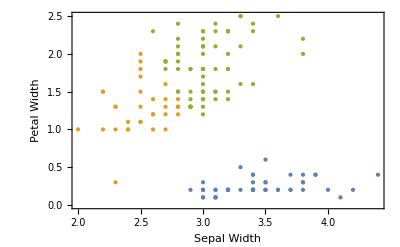
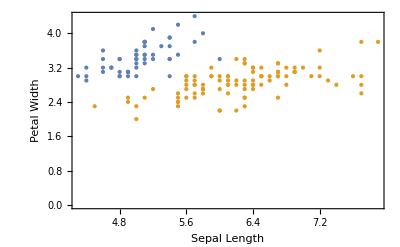
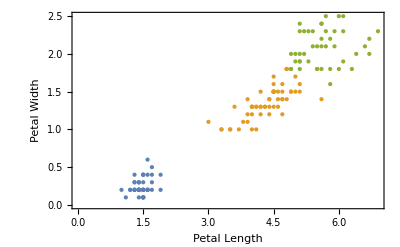

```mathematica
{ListPlot[c1,fr,ptstyle,FrameLabel->{"Sepal Width","Petal Width"}],ListPlot[c2,fr,ptstyle, FrameLabel->{"Sepal Length","Petal Width"}],ListPlot[c3,fr, ptstyle, FrameLabel->{"Petal Length","Petal Width"}]}
```

#### Petal Length and Width show a clean stratification of species class

```mathematica
subset4=Thread[{petalLength,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c4=FindClusters[subset4];

subset5=Thread[{petalWidth,class/.{"setosa"->1, "versicolor"->2, "virginica"->3}}];
c5=FindClusters[subset5];
```

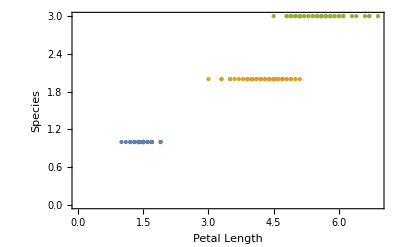
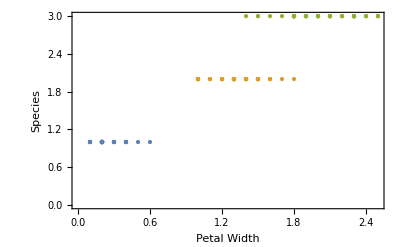

```mathematica
{ListPlot[c4,fr,ptstyle,FrameLabel->{"Petal Length","Species"}],ListPlot[c5,fr,ptstyle,FrameLabel->{"Petal Width","Species"}]}
```

## Classification, Validation and Confusion

For a certain size of training and validation data, the best (minimum speed and accuracy > 93) is  chosen

```mathematica
geomdata=Thread[{sepalLength,sepalWidth,petalLength,petalWidth}];
mldata=RandomSample[Thread[geomdata->class]];
s=Dimensions[mldata][[1]]
training=mldata[[1;;Ceiling[0.8*s]]];
validation=mldata[[Ceiling[0.8*s];;]];
```

150

#### Classification

```mathematica
ciris=Classify[training,PerformanceGoal->"Quality",Method->"DecisionTree"]
```

ClassifierFunction[…]

#### Classifier Measurements

```mathematica
cm=ClassifierMeasurements[ciris,validation]
```

ClassifierMeasurementsObject[…]

#### Accuracy and Confusion Matrix

1.

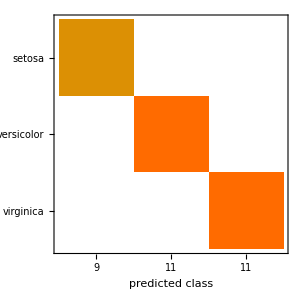

```mathematica
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

## Thermodynamics data

After using the Fisher Iris data set as a benchmark for classification and prediction accuracy, I turn my attention to a thermodynamic interpolated from IAPWS IF-97 industrial standard

```mathematica
url="http://pages.mtu.edu/~dnaneet/thermo/hptr_dense_1.txt";
datasetDirty=Import[url, "Data"];
(*names={'celcius','bar','region','kJPerKg'}*)
s=Dimensions[datasetDirty][[1]];
dataset=Select[datasetDirty, #[[3]]≠ 0&]; (*Select only those rows and columns with non zero region*)
s=Dimensions[dataset][[1]];
```

```mathematica
s
Take[dataset,5]
```

36580

{{10,1,1,42.1174},{15,1,1,63.0778},{20,1,1,84.0118},{25,1,1,104.928},{30,1,1,125.833}}

## Division of data for easy readability and clustering

#### Data wrangling

```mathematica
T=dataset[[2;;s,1]]; (*temperature, C*)
P=dataset[[2;;s,2]]; (*pressure, bar*)
r=dataset[[2;;s,3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"}; (*region, class/label*)
h=dataset[[2;;s,4]]; (*specific enthalpy, kJ/kg*)
```

#### Clustering

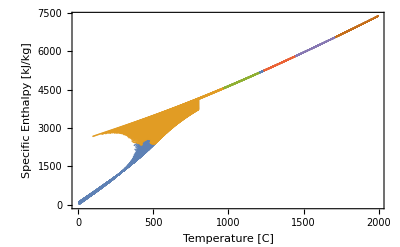

```mathematica
subset1=Thread[{T,h}];
c1=FindClusters[subset1,Method->"Spectral"];
ListPlot[c1,Frame->True,FrameStyle->Black,FrameLabel->{"Temperature [C]","Specific Enthalpy [kJ/kg]"}]
```

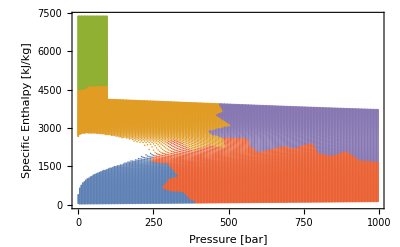

```mathematica
subset2=Thread[{P,h}];
c2=FindClusters[subset2,Method->"Spectral"];
ListPlot[c2,Frame->True,FrameStyle->Black,FrameLabel->{"Pressure [bar]","Specific Enthalpy [kJ/kg]"}]
```

```mathematica
subset3d=Thread[{P,T,h}];
c3d=FindClusters[subset3d];
```

```mathematica
ListContourPlot3D[c3d[[1]][[1;;1000]],Contours->12,PlotLegends->Automatic]//Inactivate;
```

## Classification of water/steam data

```mathematica
thermoState=Thread[{T,P}]; (*thermodynamic state*)
mldata=RandomSample[Thread[thermoState->r]]; (*state -> region*)
```

```mathematica
s=Dimensions[mldata][[1]];
training=mldata[[1;;Ceiling[0.8*s]]];
validation=mldata[[Ceiling[0.8*s];;s]];
```

```mathematica
cThermo0=Classify[training,Method->"DecisionTree"]
cThermo1=Classify[training,Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

98.8928

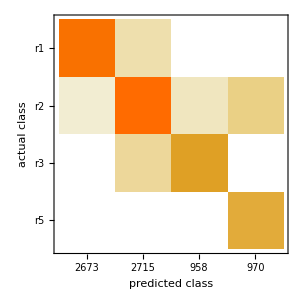

```mathematica
cm0=ClassifierMeasurements[cThermo0,validation]
cm0["Accuracy"]*100
cm0["ConfusionMatrixPlot"]
```

ClassifierMeasurementsObject[…]

99.7676

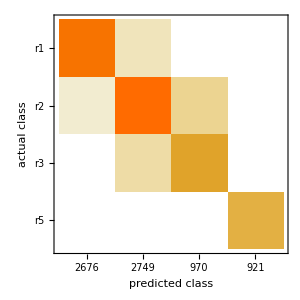

```mathematica
cm1=ClassifierMeasurements[cThermo1,validation]
cm1["Accuracy"]*100
cm1["ConfusionMatrixPlot"]
```

## Decision Tree Prediction Object

```mathematica
thermoState=Thread[{T,P}]; (*thermodynamic state*)
mldata=RandomSample[Thread[thermoState->h]]; 
s=Dimensions[mldata][[1]];
training=mldata[[1;;Ceiling[0.8*s]]]; (*90%-10% works best*)
validation=mldata[[Ceiling[0.8*s];;s]];
```

```mathematica
pThermo0=Predict[training,Method->"DecisionTree"]
pThermo1=Predict[training,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
pm0=PredictorMeasurements[pThermo0,validation]
pm1=PredictorMeasurements[pThermo1,validation]
```

PredictorMeasurementsObject[…]

PredictorMeasurementsObject[…]

## Prediction Quality

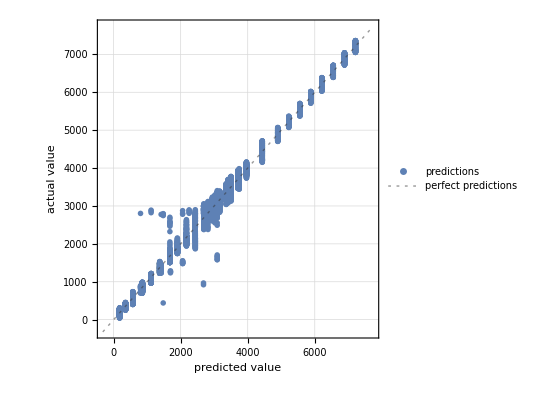
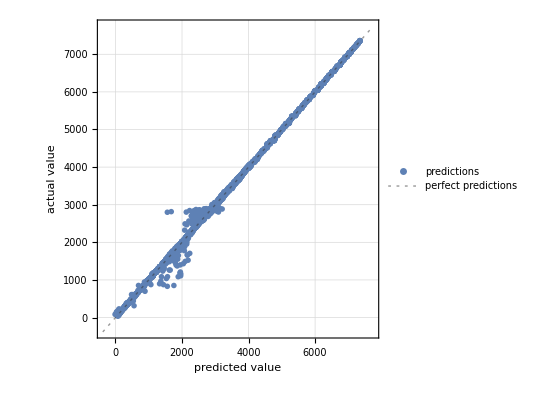

```mathematica
{pm0["ComparisonPlot"], pm1["ComparisonPlot"]}
(*wpe=pm0["WorstPredictedExamples"->25];*)
```

## Prediction of Power produced by a Steam Turbine

The state of steam at the entrance and the exit to a reversible, adiabatic turbine is (T1, P1) = (320 °C, 5000 kPa) and (T2, P2) = (99.98 °C, 100 kPa).  If the changes in specific kinetic energy and specific potential energy are negligible in comparison to change in specific enthalpy, find the useful power generated by this turbine when operating at steady state.

```mathematica
{Tin, Pin} = {320, UnitConvert[Quantity[5000,"kPa"],"Bar"][[1]]}
{Tout, Pout} = {99.98, UnitConvert[Quantity[100,"kPa"],"Bar"][[1]]//N}
```

{320,50}

{99.98,1.}

```mathematica
{hin=pThermo0[{Tin, Pin}],
hout=pThermo0[{Tout, Pout}]}
wout0 =Quantity[hin - hout,"kJ/kg"]

{hin=pThermo1[{Tin, Pin}],
hout=pThermo1[{Tout, Pout}]}
wout0 =Quantity[hin - hout,"kJ/kg"]
```

{2821.04,1384.13}

1436.9 kJ/kg

{3046.,1422.28}

1623.72 kJ/kg

```mathematica
hStan[T0_, P0_]:=Module[{T=T0,P=P0},
ThermodynamicData["Water","Enthalpy",{"Temperature"->Quantity[T,"DegreesCelcius"],"Pressure"->Quantity[P,"Bar"]}][[1]]
];
```

```mathematica
{hStan[Tin, Pin],hStan[Tout,Pout]}
```

{2.98623×10^6,2.67572×10^6}

## Enthalpy jump when change of phase occurs

#### Jump in enthalpy for an isobaric process (@1 bar)

```mathematica
(*names={'celcius','bar','region','kJPerKg'}*)
(*s=Dimensions[datasetDirty][[1]];*)
(*dataset=Select[datasetDirty, #[[3]]≠ 0&];*) (*Select only those rows and columns with non zero region*)
(*s=Dimensions[dataset][[1]];*)
Take[dataset,10]
```

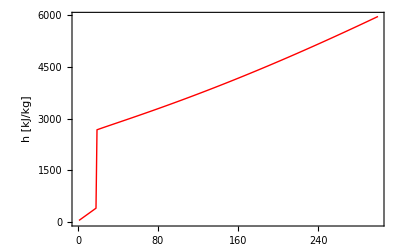

```mathematica
ListLinePlot[dataset[[1;;300,4]],Frame->True,FrameStyle->Black,FrameLabel->{"","h [kJ/kg]"},PlotStyle->{Thick,Red}]
```

```mathematica
start=4000;
end=4300;
prediction0=Table[pThermo0[{dataset[[i,1]],dataset[[i,2]]}],{i,start,end,1}];
prediction1=Table[pThermo1[{dataset[[i,1]],dataset[[i,2]]}],{i,start, end,1}];
```

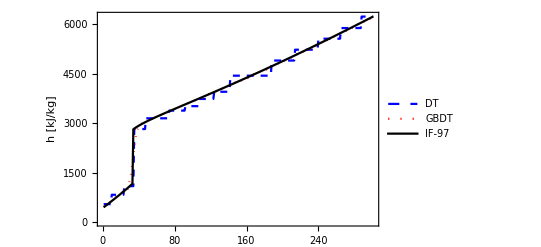

```mathematica
ListLinePlot[{prediction0, prediction1,dataset[[start;;end,4]]},Frame->True,FrameStyle->Black,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dotted,Red},{Thick,Black}},FrameLabel->{"","h [kJ/kg]"},PlotLegends->{"DT","GBDT","IF-97"}]
```

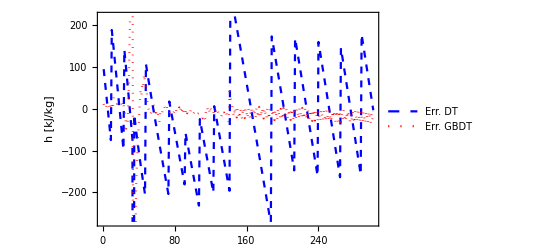

```mathematica
ListLinePlot[{prediction0-dataset[[start;;end,4]], prediction1-dataset[[start;;end,4]]},Frame->True,FrameStyle->Black,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dotted,Red}},FrameLabel->{"","h [kJ/kg]"},PlotLegends->{"Err. DT","Err. GBDT"}]
```

## C̶o̶n̶c̶l̶u̶s̶i̶o̶n̶s̶ Summary